## Задание 1 пункт а

Пробел выполняет роль знака умножения

```mathematica
9 12
```

108

## Задание 1 пункт б

Введение дополнительных пробелом не изменяют результата вычислений

```mathematica
9                12
```

108

```mathematica
9                +12
```

21

```mathematica
9                -12
```

-3

```mathematica
9                * 12
```

108

```mathematica
9                /12
```

3/4

## Задание 1 пункт в

Целые, рациональные и иррациональные числа считаются заданными точно . Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя .

```mathematica
√126
```

3 √14

```mathematica
√126.
```

11.225

```mathematica
8/9
```

8/9

```mathematica
8./9
```

0.888889

## Задание 1 пункт г

Действительные числа, содержащие десятичную точку, считаются заданными приближенно . Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды .

```mathematica
√124
```

2 √31

```mathematica
√124.
```

11.1355

```mathematica
6/9
```

2/3

```mathematica
6./9
```

0.666667

## Задание 1 пункт д

Для изменения стандартного порядка выполнения операций используются скобки

```mathematica
8(22+78)
```

800

## Задание 2 пункт а

С помощью функции N вычислить √17 с точностью до 200 значащих цифр. Провериться потом с помощью Precision.

```mathematica
N[√17,200]
Precision[%]
Precision[N[√17,200]]
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

200.

200.

## Задание 2 пункт б

Найти приближенное значение числа e^(π √163) с точностью до 40 значащих цифр . Вычислить насколько полученный результат отличается от ближайшего к нему целого числа . Для стандратного округления чисел в системе Mathematica используется функция Round[x].

```mathematica
ⅇ^(π √163)
```

ⅇ^(√163 π)

```mathematica
ⅇ^(π √163.)
```

2.62537×10^17

```mathematica
N[ⅇ^(π √163),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[N[ⅇ^(π √163),40]]
```

262537412640768744

## Задание 2 пукнт в

Вычислите (10((10.8 10^3)/300)^(1/2)+4)^(1/3);(10^-24 10^12)/10^-14 √(32768/2^9).

```mathematica
(10((10.8 10^3)/300)^(1/2)+4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

## Задание 2 пункт г

Последовательно введите выражение 5 > 3; 5 < 2.

```mathematica
5>3
```

True

```mathematica
5<2
```

False

```mathematica
π^ⅇ>ⅇ^π
```

False

```mathematica
N[π^ⅇ,6]
```

22.4592

```mathematica
N[ⅇ^π,6]
```

23.1407

## Задание 3 пункт а

Решить уравнения √(x+2)+4x=4; x^3-3 x^2+5=0.

```mathematica
Print["Количество корней: ", Length[Solve[√(x+2)+4x==4,x]]]
Solve[√(x+2)+4x==4,x]
NSolve[√(x+2)+4x==4,x]

Print["Количество действительных корней: ", Length[NSolve[√(x+2)+4x==4,x,Reals]]]
NSolve[√(x+2)+4x==4,x,Reals]
```

Количество корней: 1

{{x→1/32 (33-√193)}}

{{x→0.597111}}

Количество действительных корней: 1

{{x→0.597111}}

```mathematica
Print["Количество корней: ", Length[Solve[x^3-3 x^2+5==0,x]]]
NSolve[x^3-3 x^2+5==0,x]

Print["Количество действительных корней: ", Length[NSolve[x^3-3 x^2+5==0,x,Reals]]]
NSolve[x^3-3 x^2+5==0,x,Reals]
```

Количество корней: 3

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

Количество действительных корней: 1

{{x→-1.1038}}

## Задание 3 пункт б

Решить системы уравнений 
x^2+x y+y^2==1 иx^3+x^2 y+x y^2+y^3==4;
x-y^2+3z==24 и x+y-z==-1 и -x+2y+3z==4.

```mathematica
Print["Количество корней: ", Length[NSolve[{x^2+x y+y^2==1,x^3+x^2 y+x y^2+y^3==4}, {x,y}]]]
NSolve[{x^2+x y+y^2==1,x^3+x^2 y+x y^2+y^3==4}, {x,y}]

Print["Количество действительных корней: ", Length[NSolve[{x^2+x y+y^2==1,x^3+x^2 y+x y^2+y^3==4}, {x,y},Reals]]]
NSolve[{x^2+x y+y^2==1,x^3+x^2 y+x y^2+y^3==4}, {x,y},Reals]
```

Количество корней: 6

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

Количество действительных корней: 0

{}

```mathematica
Print["Количество корней: ", Length[NSolve[{x-y^2+3z==24,x+y-z==-1,-x+2y+3z==4}, {x,y,z}]]]
NSolve[{x-y^2+3z==24,x+y-z==-1,-x+2y+3z==4}, {x,y,z}]

Print["Количество действительных корней: ", Length[NSolve[{x-y^2+3z==24,x+y-z==-1,-x+2y+3z==4}, {x,y,z}, Reals]]]
NSolve[{x-y^2+3z==24,x+y-z==-1,-x+2y+3z==4}, {x,y,z},Reals]
```

Количество корней: 2

{{x→9.25-6.49519 ⅈ,y→-3.5+2.59808 ⅈ,z→6.75-3.89711 ⅈ},{x→9.25+6.49519 ⅈ,y→-3.5-2.59808 ⅈ,z→6.75+3.89711 ⅈ}}

Количество действительных корней: 0

{}

## Задание 3 пункт в

Придумайте уравнение или систему полиминальных уравнений и найдите ее численное решение .

```mathematica
Print["Количество действительных корней: ", NSolve[{3x-y==2,3x-2y==9},{x,y}]]
Solve[{3x-y==2,3x-2y==9},{x,y}]
NSolve[{3x-y==2,3x-2y==9},{x,y}]

Print["Количество действительных корней: ", Length[NSolve[{3x-y==2,3x-2y==9},{x,y}, Reals]]]
NSolve[{3x-y==2,3x-2y==9},{x,y}, Reals]
```

Количество действительных корней: {{x→-1.66667,y→-7.}}

{{x→-5/3,y→-7}}

{{x→-1.66667,y→-7.}}

Количество действительных корней: 1

{{x→-1.66667,y→-7.}}

## Задание 4 (вариант 5) номер 5

Используя функцию FindRoot, найти решения следующих уравнений:
5) ⅇ^x = 3 cos(x) на отрезке x c [-2;2]

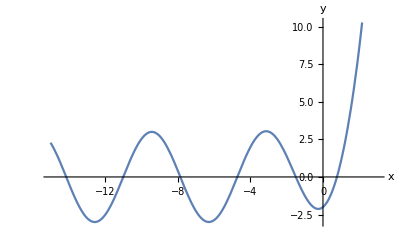

```mathematica
Plot[ⅇ^x==3Cos[x], {x,-15,3}, AxesLabel->{"x","y"}]
```

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,0,5}]
```

{x→0.768579}

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,-3,0}]
```

{x→-1.49606}

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,-7,-3}]
```

{x→-4.71537}

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,-10,-7}]
```

{x→-7.85385}

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,-13,-10}]
```

{x→-10.9956}

```mathematica
FindRoot[ⅇ^x==3Cos[x],{x,-15,-13}]
```

{x→-14.1372}

## Задание 5 (вариант 5) номер 5

Найдите решение одного из следующих дифференциальных уравнений на заданном отрезке.
5. y’’[x]+x y[x]-Cos[2x]=0, y[0]=0, y’[0]=2 на отрезке x c [0;5]

Для численного решения дифференциальных уравнений и их систем имеется функция NDSolve, которая вызывается по крайней мере с тремя аргументами
NDSolve[eqns, y, {x, xmin, xmax}]
eqns - список, который включает дифференциальное уравнение и необходимое число граничных или начальных условий
y - имя функция, относительно которой решается уравнение
x - имя независимой переменной, причём решение ищется на отрезке от xmin до xmax

```mathematica
Print[
"Колитчество решений: ",
Length[NDSolve[{y''[x]+x y[x]-Cos[2x]==0,y[0]==0,y'[0]==2}, y, {x,0,5}]]
]
sol = NDSolve[{y''[x]+x y[x]-Cos[2x]==0,y[0]==0,y'[0]==2}, y, {x,0,5}]
```

Колитчество решений: 1

{{y→InterpolatingFunction[…]}}

Чтобы найти корни уравнения y(x)=0, построим график найденной функции.

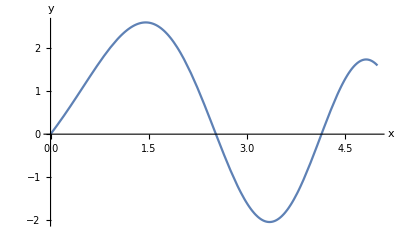

```mathematica
Plot[y[x]/.sol, {x,0,5},AxesLabel->{"x","y"}]
```

```mathematica
FindRoot[y[x]/.sol,{x,0,1}]
```

{x→0.}

```mathematica
FindRoot[y[x]/.sol,{x,2,3}]
```

{x→2.52928}

```mathematica
FindRoot[y[x]/.sol,{x,4,5}]
```

{x→4.14386}

## Задание 6 пункт а

а)Задайте произвольные численные значения параметров a, b, c, d, e в следующих зависимостях:
y(x) = a +bc + c x^2 + d x^3 + e x^4
y(x) = a +bc + c sin(x) + d cos(x)
y(x) = a +bc + c sin(x) + d cos(2x)
y(x) = a sin(x) +b cos(x) + c sin(2x) + d cos(2x)
Используя функцию Table, определите список численных данных, каждый элемент которого содержит два соотвествующих элемента (x, y). Область изменения x и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке x случайное возмущение ⚠y.
б)

```mathematica
For[i=0, i < 10, i+= 1,Print[Random[Real, {-0.2, 0.2}]]]
```

0.154184

-0.165853

-0.192904

-0.025182

-0.0781497

-0.0483004

-0.0582308

-0.0949683

0.041006

-0.0894488

```mathematica
a=4;b=5;c=6;d=7;e=8;

tab1 = Table[
{
x,
(a+b c + c x^2+d x^3+e x^4)*(1+Random[Real, {-0.2, 0.2}])
},
{x, 0,10,0.25}
]

tab2 = Table[
{
x,
(a+b c + c Sin[x]+d Cos[x])*(1+Random[Real, {-0.2, 0.2}])
},
{x, 0,10,0.25}
]

tab3= Table[
{
x,
(a+b c + c Sin[x]+d Cos[2 x])*(1+Random[Real, {-0.2, 0.2}])
},
{x, 0,10,0.25}
]

tab4 = Table[
{
x,
(a Sin[x]+b Cos[x] + c Sin[2 x]+d Cos[2 x])*(1+Random[Real, {-0.2, 0.2}])
},
{x, 0,10,0.25}
]
```

{{0.,34.5037},{0.25,28.0204},{0.5,41.7857},{0.75,46.0358},{1.,54.8614},{1.25,67.4457},{1.5,93.0335},{1.75,190.107},{2.,231.693},{2.25,356.225},{2.5,568.731},{2.75,640.998},{3.,791.925},{3.25,1087.83},{3.5,1356.59},{3.75,2108.04},{4.,2804.2},{4.25,2867.35},{4.5,4051.89},{4.75,5090.},{5.,5673.9},{5.25,6584.12},{5.5,9914.4},{5.75,10683.3},{6.,13605.3},{6.25,12643.6},{6.5,13296.7},{6.75,22162.1},{7.,20273.},{7.25,20362.6},{7.5,33588.1},{7.75,26321.4},{8.,42901.},{8.25,41032.8},{8.5,38159.},{8.75,55741.5},{9.,64538.3},{9.25,58582.1},{9.5,84404.2},{9.75,67619.1},{10.,73853.1}}

{{0.,34.2135},{0.25,41.5045},{0.5,44.4028},{0.75,47.8052},{1.,48.4539},{1.25,43.6803},{1.5,48.4044},{1.75,45.7951},{2.,38.001},{2.25,35.5093},{2.5,26.6568},{2.75,31.6249},{3.,28.734},{3.25,28.0609},{3.5,20.8778},{3.75,27.1553},{4.,20.8758},{4.25,26.6066},{4.5,25.4208},{4.75,33.4458},{5.,34.2488},{5.25,34.5884},{5.5,31.3166},{5.75,42.1722},{6.,42.8862},{6.25,36.0874},{6.5,45.0601},{6.75,35.8275},{7.,50.4414},{7.25,44.7205},{7.5,45.1612},{7.75,34.5682},{8.,36.0844},{8.25,29.6883},{8.5,35.9738},{8.75,31.9251},{9.,33.0419},{9.25,26.5379},{9.5,27.0072},{9.75,27.8711},{10.,26.3291}}

{{0.,45.0853},{0.25,35.9226},{0.5,45.2104},{0.75,43.4517},{1.,30.1054},{1.25,39.5796},{1.5,38.7241},{1.75,27.6042},{2.,40.0621},{2.25,33.159},{2.5,45.0128},{2.75,35.5019},{3.,37.6798},{3.25,40.897},{3.5,40.44},{3.75,37.4002},{4.,25.6106},{4.25,28.7441},{4.5,19.5587},{4.75,17.5659},{5.,25.9025},{5.25,24.5166},{5.5,29.9118},{5.75,33.5273},{6.,32.8063},{6.25,36.6179},{6.5,45.4689},{6.75,42.9239},{7.,32.0918},{7.25,34.1444},{7.5,38.4402},{7.75,33.8685},{8.,29.1263},{8.25,29.2564},{8.5,43.6115},{8.75,37.792},{9.,48.0801},{9.25,42.7618},{9.5,36.2253},{9.75,38.7294},{10.,35.9266}}

{{0.,12.602},{0.25,17.7674},{0.5,15.0315},{0.75,14.3025},{1.,7.65783},{1.25,3.32962},{1.5,-1.42042},{1.75,-5.91618},{2.,-9.00818},{2.25,-8.10954},{2.5,-5.19762},{2.75,-2.43514},{3.,0.695431},{3.25,3.21381},{3.5,3.58352},{3.75,1.58574},{4.,-1.39133},{4.25,-6.26487},{4.5,-8.70513},{4.75,-11.04},{5.,-13.6627},{5.25,-10.4489},{5.5,-6.05026},{5.75,0.448715},{6.,5.93901},{6.25,12.6627},{6.5,14.0298},{6.75,12.2168},{7.,11.2083},{7.25,8.45587},{7.5,3.83846},{7.75,-1.05443},{8.,-4.42749},{8.25,-7.52255},{8.5,-8.84133},{8.75,-6.40274},{9.,-2.78062},{9.25,0.303196},{9.5,2.1123},{9.75,3.08152},{10.,2.32885}}

## Задание 6 пункт б

Изобразите полученные точки на координатной плоскости

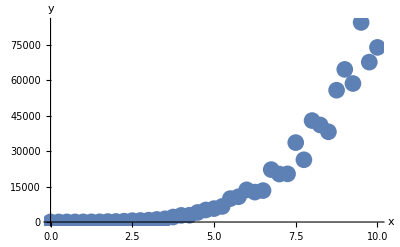
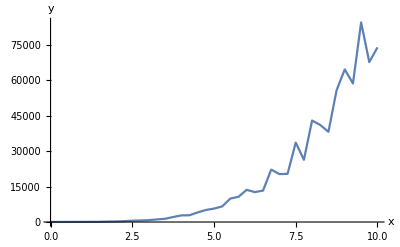

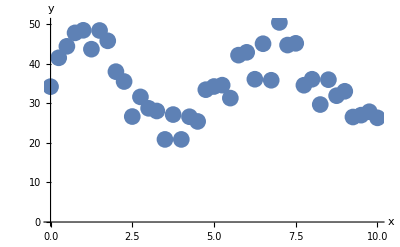
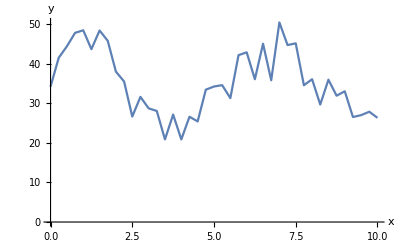

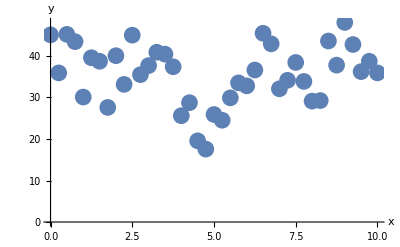
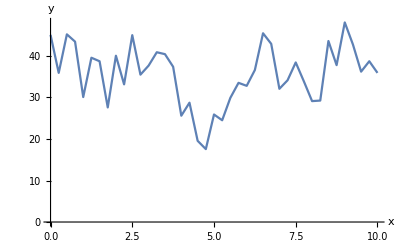

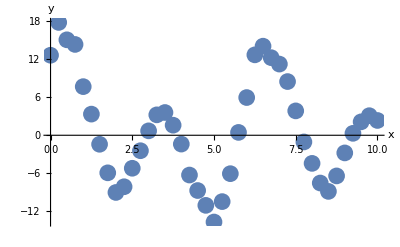
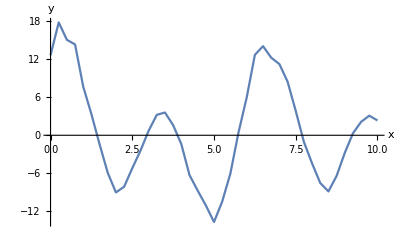

```mathematica
{
ListPlot[tab1,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}],
ListLinePlot[tab1,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
}
{
ListPlot[tab2,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}],
ListLinePlot[tab2,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
}
{
ListPlot[tab3,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}],
ListLinePlot[tab3,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
}
{
ListPlot[tab4,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}],
ListLinePlot[tab4,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
}
```

## Задание 6 пункт в

С помощью функции Fit найдите наилутшую кривую, аппроксимирующую численные данные.

```mathematica
y1=Fit[tab1, {1,x,x^2,x^3,x^4},x]
y2=Fit[tab2, {1,x,Sin[x],Cos[x]},x]
y3=Fit[tab3, {1,x,Sin[x],Cos[2x]},x]
y4=Fit[tab4, {Sin[x],Cos[x],Sin[2x],Cos[2x]},x]
```

-1243.49+3549.63 x-1919.85 x^2+350.398 x^3-11.2479 x^4

35.4872-0.165502 x+7.24444 Cos[x]+6.07715 Sin[x]

34.5166-0.0780338 x+6.86849 Cos[2 x]+6.0668 Sin[x]

4.98599 Cos[x]+7.26852 Cos[2 x]+3.96164 Sin[x]+6.11254 Sin[2 x]

## Задание 6 пункт г

На данной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками.

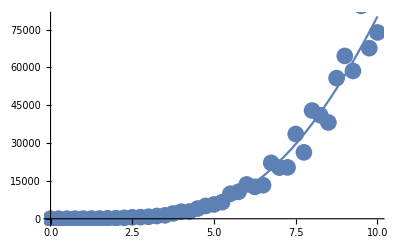

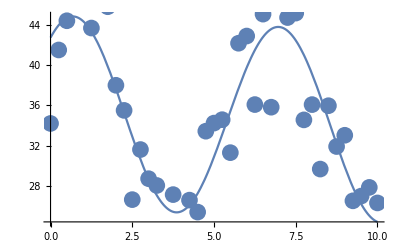

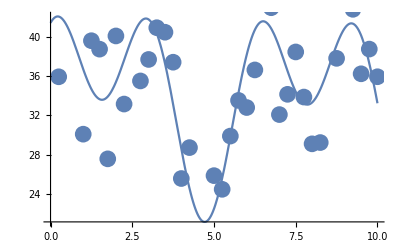

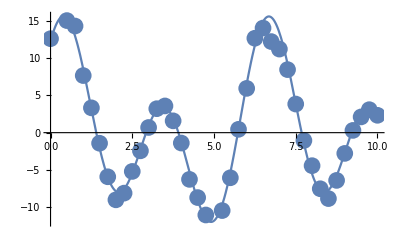

```mathematica
Show[
Plot[{y1}, {x,0,10}],
ListPlot[tab1,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
]

Show[
Plot[{y2}, {x,0,10}],
ListPlot[tab2,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
]

Show[
Plot[{y3}, {x,0,10}],
ListPlot[tab3,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
]

Show[
Plot[{y4}, {x,0,10}],
ListPlot[tab4,PlotStyle->PointSize[0.03], AxesLabel->{"x", "y"}]
]
```